```mathematica
PMatrix = Import["/Users/angelagraf/Desktop/main/AtomIon1D/P_Matrix.dat","Table"];
QMatrix = Import["/Users/angelagraf/Desktop/main/AtomIon1D/Q_Matrix.dat","Table"];
energies = Transpose[Import["/Users/angelagraf/Desktop/main/AtomIon1D/energiesv2.dat","Table"]];
RSteps = 1000;
NumStates = Length[PMatrix[[2]]];
A=1.660539 10^-27;
ma=6.015122 A;
mi=170.936323 A;
ωs=2π 300000;
C4= 1.121 10^-56;
C6=2.804 10^-75;
ℏ=1.054571817 10^-34;
mu2=(ma mi)/(ma+mi)
mu=Sqrt[ma/mi]
thetaC = ArcTan[mu];
aho=Sqrt[ℏ/(ωs mi)]
R = Flatten[Table[PMatrix[[i+((i-1)*NumStates)]],{i,1,RSteps}]];
P = Table[Table[PMatrix[[iR+(iR-1)*NumStates + i]],{i, 1, NumStates}],{iR, 1, RSteps}];
Q = Table[Table[QMatrix[[iR+(iR-1)*NumStates + i]],{i, 1, NumStates}],{iR, 1, RSteps}];
PlotP[i_,j_,R_,P_]:=Module[{f},f=Table[{R[[iR]],(P[[iR]][[i,j]])^2/(Abs[(energies[[j+1,iR]]-energies[[i+1,iR]])]*2 mu)},{iR,1,RSteps}]]
PlotPog[i_,j_,R_,P_]:=Module[{f},f=Table[{R[[iR]],P[[iR]][[i,j]]},{iR,1,RSteps}]]
(*PlotQ[i_,j_,R_,Q_]:=Module[{f},f=Table[{R[[iR]],Q[[iR]][[i,j]](*energies[[j+1,iR]]-energies[[i+1,iR]]*)},{iR,1,RSteps}]]*)
```

9.64881×10^-27

0.187588

1.40393×10^-8

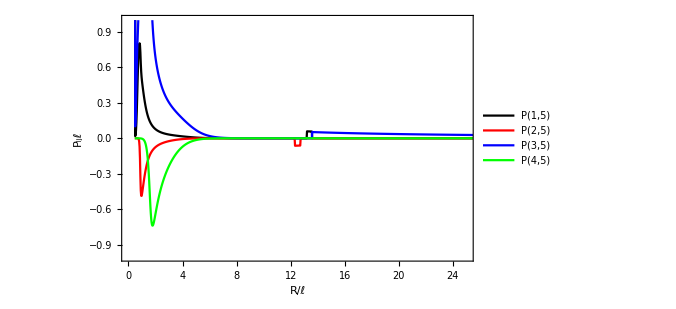

```mathematica
Needs["PlotLegends`"];
ListPlot[{PlotPog[1,5,R,P], PlotPog[2,5,R,P], PlotPog[3,5,R,P], PlotPog[4,5,R,P]},  PlotRange->{{0,25},{-1,1}}, Joined -> True, Frame -> True, FrameLabel -> {"R/ℓ","P_ijℓ"}, LabelStyle->Large, PlotLegends->{"P(1,5)","P(2,5)","P(3,5)","P(4,5)"}, PlotStyle -> {{Black},{Red},{Blue},{Green}}, ImageSize -> {500,500}](*Epilog -> {Inset[ListPlot[{PlotPog[1,5,R,P], PlotPog[2,5,R,P], PlotPog[3,5,R,P], PlotPog[4,5,R,P]},  PlotRange->{{1,30},{-1,1}}, Joined -> True, Frame -> True, PlotStyle -> {{Black},{Red},{Blue},{Green}}, ImageSize -> {200,200}],{4.5,0.2},{0,0}]}]
ListPlot[PlotPog[79,4,R,P], Joined -> True, PlotRange-> {{0,30},{-1,1}}]*)
```